## Various interactions with ALPs

## Definitions

```mathematica
DΣ4alp[x_,μ_]=dΣ4[x,μ]+dalp[x,μ]*(Σ4[x].ChiralRotationCoefficientHC+ChiralRotationCoefficientHC.Σ4[x]);
DΣ4alpHC[x_,μ_]=ConjugateTranspose[DΣ4alp[x,μ]];
(*Given the transformation Σ->Exp[-Subscript[ic, G]κ a/Subscript[f, a]]×Σ×Exp[-Subscript[ic, G]κ a/Subscript[f, a]] and using Σ=Exp[i*2/Subscript[f, π] P], it may be possible to find the transformation of P assuming Subscript[f, π]/Subscript[f, a] << 1, and then revert it*)
(*BCH formula is used*)
(*The part with the anticommutator is commented out because it does not contribute to the processes of interest and actually belongs to the quadratic part of the expansion*)

PmatrixALP[x_]=With[{α=2/fπ,β=ChiralRotationCoefficient*alp[x]},1/(I*α)(I*α*Pmatrix[x]-I*KL*alp[x]+I*KR*alp[x](*(2*β(*+I*α*(Pmatrix[x].β+β.Pmatrix[x])*))*))]//Simplify;
dPmatrixALP[x_,μ_]=D[PmatrixALP[x],x]/.Evaluate[DerivativesReplacementRulePS[μ]];
```

## Decays of kaons

```mathematica
WeakDecaysTermALP=G8*fπ^4*ruleLeavingPower[Tr[(DiagonalMatrix[{1,1,1}]+ChiralRotationCoefficientHC*alp[x]).λmatrix.(DiagonalMatrix[{1,1,1}]+ChiralRotationCoefficient*alp[x]).DΣ4alpHC[x,μ].DΣ4alp[x,μ]],4];
WeakDecaysTermALP=(WeakDecaysTermALP/.{ϵ->0})+(D[WeakDecaysTermALP,ϵ]/.{ϵ->0})*ϵ//Expand;
WeakDecaysTermALP=WeakDecaysTermALP+Conjugate[WeakDecaysTermALP]//Expand;
```

## VMD Lagrangian

```mathematica
(*Expression from https://arxiv.org/pdf/1111.5949.pdf for Subscript[c, 3] = Subscript[c, 1]-Subscript[c, 2] = 1*)
VMDtermALP1=ruleLeadingOrderIsospin[(gVVP*EPSILON[μ,ν,α,β]*2*Tr[PmatrixALP[x].dVmatrix[x,μ,ν].dVmatrix[x,α,β]]+3/(240 Pi^2 fπ^5)(1-15/8)EPSILON[μ,ν,α,β]*2^5 Tr[PmatrixALP[x].dPmatrixALP[x,μ].dPmatrixALP[x,ν].dPmatrixALP[x,α].dPmatrixALP[x,β]])];//AbsoluteTiming
VMDtermALP1=(VMDtermALP1/.ϵ->0)+(D[VMDtermALP1,ϵ]/.{ϵ->0})*ϵ//Expand;//AbsoluteTiming
VMDtermALP2=ruleLeadingOrderIsospin[cvmd*UnitStep[mηpr-ma]/(2 fπ^2)*Tr[(PmatrixALP[x].dPmatrixALP[x,μ]-dPmatrixALP[x,μ].PmatrixALP[x]).(dPmatrixALP[x,μ].PmatrixALP[x]-PmatrixALP[x].dPmatrixALP[x,μ])]-I*2*gval*Tr[Vmatrix[x,μ].(PmatrixALP[x].dPmatrixALP[x,μ]-dPmatrixALP[x,μ].PmatrixALP[x])]];//AbsoluteTiming
VMDtermALP2=(VMDtermALP2/.ϵ->0)+(D[VMDtermALP2,ϵ]/.{ϵ->0})*ϵ//Expand;//AbsoluteTiming
VMDtermALP=((VMDtermALP1+VMDtermALP2)/.{ρ0[x,μ_]:>ρ0[x,μ]+VA["ρ^0"]*A[x,μ],dρ0[x,μ_,ν_]:>dρ0[x,μ,ν]+VA["ρ^0"]*dA[x,μ,ν],ϕ[x,μ_]:>ϕ[x,μ]+VA["ϕ"]*A[x,μ],dϕ[x,μ_,ν_]:>dϕ[x,μ,ν]+VA["ϕ"]*dA[x,μ,ν],ω[x,μ_]:>ω[x,μ]+VA["ω"]*A[x,μ],dω[x,μ_,ν_]:>dω[x,μ,ν]+VA["ω"]*dA[x,μ,ν]}//Expand)+LmassKineticVMD;
Conjugate[coef1]^:=coef1
```

{0.0042073,Null}

{0.584934,Null}

{0.0012618,Null}

{0.0360912,Null}

## Scalar mesons

```mathematica
LscalarAalp=CoefA*(2*Tr[Smatrix[x].dPmatrixALP[x,μ].dPmatrixALP[x,μ]]-Tr[Smatrix[x]]*Tr[dPmatrixALP[x,μ].dPmatrixALP[x,μ]]-2*Tr[Smatrix[x].dPmatrixALP[x,μ]]*Tr[dPmatrixALP[x,μ]]+Tr[Smatrix[x]]*Tr[dPmatrixALP[x,μ]]*Tr[dPmatrixALP[x,μ]]);
LscalarBalp=CoefB*Tr[Smatrix[x]]*Tr[dPmatrixALP[x,μ].dPmatrixALP[x,μ]];
LscalarCalp=CoefC*Tr[Smatrix[x].dPmatrixALP[x,μ]]*Tr[dPmatrixALP[x,μ]]//Expand//Simplify;
LscalarDalp=CoefD*Tr[Smatrix[x]]*Tr[dPmatrixALP[x,μ]]*Tr[dPmatrixALP[x,μ]]//Expand//Simplify;
{LscalarAalp,LscalarBalp,LscalarCalp,LscalarDalp}=((#/.{ϵ->0})+(D[#,ϵ]/.{ϵ->0})ϵ//Expand//Simplify//Expand)&/@{LscalarAalp,LscalarBalp,LscalarCalp,LscalarDalp};
LscalarALP=LscalarAalp+LscalarBalp+LscalarCalp+LscalarDalp;
```

## Tensor mesons

```mathematica
DΣ1alp[x_,μ_]=dΣ1[x,μ]+dalp[x,μ]*(Σ1[x].ChiralRotationCoefficientHC+ChiralRotationCoefficientHC.Σ1[x]);
DΣ1alpHC[x_,μ_]=ConjugateTranspose[DΣ1alp[x,μ]];
(*So far, only Subscript[f, 2] PP terms. From A.26 of 2110.10691*)
(*Similar to 2110.10691 and 1811.03474, only the first order expansion of Σ in terms of P is used*)
LagrangianTalp=-gT*fπ^2/4(2*TfieldSymbol["f_2",x,μ,ν]*Tr[DiagonalMatrix[{1/2,1/2,0}].(DΣ1alpHC[x,μ].DΣ1alp[x,ν]-1/2*mt[μ,ν]*DΣ1alpHC[x,α].DΣ1alp[x,α])]);
LagrangianTalp=(LagrangianTalp/.{ϵ->0})+(D[LagrangianTalp,ϵ]/.{ϵ->0})*ϵ//Expand//Simplify;
```

## Nucleons

(ϵ (6 cG (DD (-κd)+DD+DDs+F (κd+2 κu-1))+3 √3 DD ηprALP+3 DD π0ALP+√6 DDs ηALP+4 √3 DDs ηprALP+2 √6 F ηALP-√3 F ηprALP+3 F π0ALP))/(6 fπ)

0

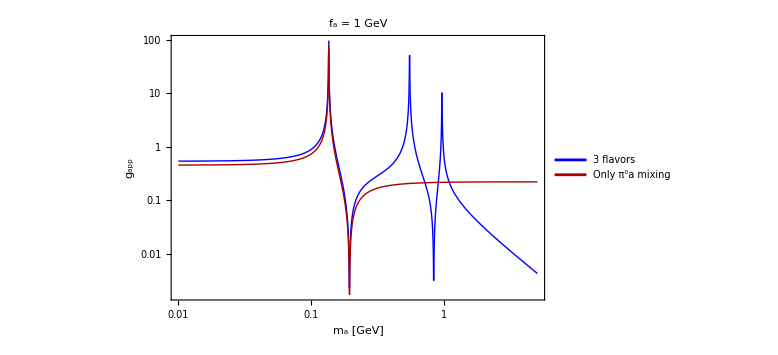

```mathematica
gaNNsymbolic=1/fπ((DDs*κd*cG*ϵ+(DD+DDs-F)(1-κu-κd)*cG*ϵ+cG*ϵ*κu*(DD+DDs+F))+ϵ/2((DD+F)π0ALP-1/(√3)(DD-3F)(eta8/.etasols)+√(2/3)(2DD+3DDs)(eta0/.etasols)))/.{η[x]->ηALP,ηpr[x]->ηprALP}/.replθηηPr//Simplify
test1=gaNNsymbolic/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{cu->0,cd->0,cs->0}//Simplify;
D[test1,κu]κu+D[test1,κd]κd/.{mηpr^2->M2relationPureChPT["η'"]}//Simplify
gaNNexplicit[ma_,cu_,cd_,cs_,cG_,ϵ_]=Simplify[gaNNsymbolic/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{mηpr^2->M2relationPureChPT["η'"]}]/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2}//Expand//Simplify;
gaNNnumeric[ma_,cu_,cd_,cs_,cG_,fa_]=ruleSymbolsToNumbersFinal[gaNNexplicit[ma,cu,cd,cs,cG,ϵ],2]/.{F->0.46,DD->0.8,DDs->-0.41}//Simplify;
tabCouplings[ma_,fa_]=gaNNnumeric[ma,cRGval[#,10^3.,"cu"],cRGval[#,10^3.,"cu"],cRGval[#,10^3.,"cu"],cRGval[#,10^3.,"cG"],fa]&/@{"Fermion universal","Gluon"};
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"auxiliary data/appCouplings.mx"}],{{"ALP-fermion","ALP-gluon"},tabCouplings[ma,fa]}//Transpose,"MX"];
gaNNexplicit1[ma_,cu_,cd_,cs_,cG_,ϵ_]=Simplify[gaNNsymbolic/.rulem0aTransformationSymbolicToExplicit["Only π^0a"]/.{mηpr^2->M2relationPureChPT["η'"]}]/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2}//Expand//Simplify;
gaNNnumericOnlyπ0aMixing[ma_,cu_,cd_,cs_,cG_,fa_]=ruleSymbolsToNumbersFinal[gaNNexplicit1[ma,cu,cd,cs,cG,ϵ]/.{κu->1-κd},2]/.{F->0.46,DD->0.8,DDs->-0.41}//Simplify;
LogLogPlot[{Abs[gaNNnumeric[ma,0,0,0,1,1]],Abs[gaNNnumericOnlyπ0aMixing[ma,0,0,0,1,1]]},{ma,0.01,5},PlotRange->All,ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,20],FrameLabel->{"m_a [GeV]","g_app"},PlotLabel->Style[Row[{"f_a = 1 GeV"}],18,Black],PlotLegends->Placed[Style[#,18]&/@{"3 flavors","Only π^0a mixing"},{0.2,0.8}],PlotStyle->{{Thick,Blue},{Thick,Darker@Red}}]
```